```mathematica
DSolve[{y'[t]==3*y[t]+3*t,y[0]==1},y[t],{t,0,2}]
```

{{y[t]→1/3 (-1+4 ⅇ^(3 t)-3 t)}}

```mathematica
{{y[t]->1/3 (-1+4 ⅇ^(3 t)-3 t)}}/.Rule->Equal
```

{{y[t]==1/3 (-1+4 ⅇ^(3 t)-3 t)}}

```mathematica
{{y[t]->1/3 (-1+4 ⅇ^(3 t)-3 t)}}⟦1,1,2⟧
```

1/3 (-1+4 ⅇ^(3 t)-3 t)

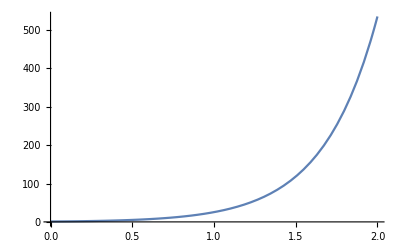

```mathematica
Plot[-1/3-t+(4/3)*Exp[3*t],{t,0,2}]
```

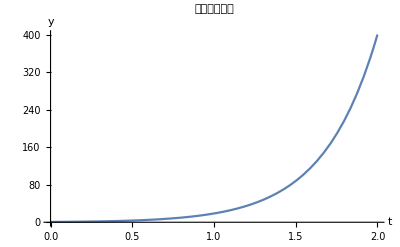

```mathematica
Show[%7,AxesLabel->{HoldForm[t],HoldForm[y]},PlotLabel->HoldForm[精确解的图形],LabelStyle->{FontFamily->"Arial",16,GrayLevel[0],Bold}]
```

```mathematica
Export["E:\\MyMathMa\\figure.png",%8,"PNG"]
```

E:\MyMathMa\figure.png

```mathematica
Plot[-1/3-t+(4/3)*Exp[3*t],{t,0,2}]
```

-Graphics-